# Arm state visualization

## Import

```mathematica
(*ClearAll["Global`*"]
Clear["Global`*"]*)

AppendTo[$Path,"/Users/thomasbuhrmann/Library/Mathematica/Packages/LevelScheme"];
Get["LevelScheme`"];

(* Best *)
dirNameB1 = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_01_16__12_26_42"; (* Mv1234 0.994 *)
dirNameB2 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_12_04__17_49_45"; (* Mv1234 0.992 *)
dirNameB3 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_11_30__13_57_40"; (* Mv24 0.9918 *)
dirNameB4 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_11_27__21_30_56"; (* Mv1234 0.9928 *)
dirNameB5 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_11_19__21_52_30"; (* Mv1234 0.9918 *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_03_21__13_38_43"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_11__17_43_03"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_25__14_55_44"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_26__15_44_55"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_27__00_48_28"; (* *)

(* Ablation *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_29__11_19_24"; (* Best: Inc from 13_04_27__13_03_45: 0.9897 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_30__14_01_20"; (* Like above, but without IbInterseg: 0.984 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_30__19_52_19"; (* Like above, but without IbIaExc: 0.975 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_05_23__10_26_30"; (* Like above, but no Ib at all: 0.970 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_11__15_48_55"; (* No interneurons at all, but GO sig *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_12__21_00_10"; (* No interneurons at all: 0.946 *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_05_09__20_37_11"; (* Mv123456 Run from _19_47_32 *)

(* Dirs 8M *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_13__16_02_25"; (* 8M: 0.946. Soso.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_15__02_07_37"; (* 8M: 0.95. Soso.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_19__20_45_29/"; (* 0.961 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_21__11_58_38/"; (* 0.965 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_08_20__16_48_48"; (* 8M_2: 0.952. Not good. *)

(* Dirs 6M *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_15__19_15_19"; (* 6M_1: 0.967. Two moves bad. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_16__10_04_00"; (* 6M_1 inc: 0.9723. Still two bad. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_17__14_13_56"; (* 6M_1 inc2: 0.987. Pretty good. *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_07_19__11_25_57/"; (* 6M_2: 0.967. Two moves bad again. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_07_19__13_22_34/"; (* 6M_2: 0.9685. Two moves bad again. *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_12__19_54_14/"; (*!! 6M_3: 0.989.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_12__19_57_09/"; (* 6M_3: 0.9889.*)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_13__13_54_02"; (* 6M_3: 0.979.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_13__13_54_11"; (* 6M_3: 0.976.*)


dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_14__10_31_25/"; (* 6M_3: 0.983. Weird hook. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_14__00_06_01/"; (* 6M_3: 0.9825. Weird hook*)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_14__13_57_34/"; (*!! 6M_3: 0.98.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_14__13_49_02/"; (* 6M_3: 0.9785.*)

(* Dirs 4M *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_10__08_33_31"; (*!! 4M diag: 0.9916 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_10__08_33_29"; (*!! 4M diag: 0.9914 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Dirs/0/13_07_08__16_18_21/"; (* 4M straight, slow: 0.991. Wobbly. *)
(* Mv1234 check whether 4M net works for 1234: 0.96011, 0.946. No! *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_11__15_48_55/"; 
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_12__21_00_10/"; 

(* Energy min *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirsOlOn/0/13_07_18__18_39_18/"; 
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirsOlOn/0/13_07_19__09_46_01/"; (* network: 1.98171 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirsOlOn/0/13_07_19__10_56_15/"; (* network asymsp: 1.98431 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/R1/13_07_19__11_40_37/";(* network symsp noVelRef: 1.98415 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/R1/13_07_19__14_11_55/";(* R1 network symsp noVelRef: 1.9839 *)


dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__10_06_33/"; (* Engy min PD: 1.982 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_26_06/"; (* Engy min PD noVelRef: 0.993 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_33_04/"; (* Engy min PD noVelRef dbgain: 0.9934 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_46_28/"; (* Engy min PD noVelRef higher gain: 0.994 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_52_51/"; 
(* Engy min PD noVelRef higher gain, exp:  *)

(* PD control multiple movements *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs4M/13_08_20__14_11_48/"; (* 4M PD: 0.99.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_20__15_56_46/"; (* 6M PD: 0.99.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs4M/13_08_20__14_11_48/"; (* 4M PD: 0.99.*)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs4M/13_08_20__20_53_06"; (* 4M PD min engy: *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_12__21_00_10"; (* No interneurons at all: 0.946 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_29__11_19_24"; (* Best: Inc from 13_04_27__13_03_45: 0.9897 *)

(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_02_06__22_44_11";*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_12_21__15_16_27"; (* Mv1234 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_12_17__17_18_17"; (* Mv1234 *)*)

(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_19__19_38_08"; (* Mv34 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_18__14_18_53"; (* Mv12 Ext OL *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_17__15_14_34"; (* Mv12 Norm OL *)*)

(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_16__17_44_26"; (* Mv2 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_06_10__02_25_24"; (* Mv2 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_04_12__19_20_02/"; (* Mv2 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_04_13__13_03_05/"; (* Mv1 *)*)

figExpPath="~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/";
SetDirectory[dirName];
all=Import["State.txt", "Table"];
varNames=all[[1]]
data = all[[2;;-2]];
numVars=Dimensions[varNames];
numData=Length[data]

fitXml = Import["GA_Progress.xml"];
fitness=Cases[fitXml,XMLElement["Generation",{_,"BestFitness"->fit_,_},___]->fit,Infinity];
fitness=ToExpression[fitness];
font="Arial";
```

LevelScheme scientific figure preparation system
M. A. Caprio, Department of Physics, University of Notre Dame
Comput. Phys. Commun. 171, 107 (2005)
Version 3.53 (January 10, 2013)
View color paletteVisit home page  -Graphics-

{ElbowExtensorAct,ElbowExtensorForce,ElbowExtensorFrcAct,ElbowExtensorFrcPsv,ElbowExtensorFrcVel,ElbowExtensorLengthNorm,ElbowExtensorMomentArm,ElbowExtensorTorque,ElbowExtensorVelocityNorm,ElbowFlexorAct,ElbowFlexorForce,ElbowFlexorFrcAct,ElbowFlexorFrcPsv,ElbowFlexorFrcVel,ElbowFlexorLengthNorm,ElbowFlexorMomentArm,ElbowFlexorTorque,ElbowFlexorVelocityNorm,ShoulderExtensorAct,ShoulderExtensorForce,ShoulderExtensorFrcAct,ShoulderExtensorFrcPsv,ShoulderExtensorFrcVel,ShoulderExtensorLengthNorm,ShoulderExtensorMomentArm,ShoulderExtensorTorque,ShoulderExtensorVelocityNorm,ShoulderFlexorAct,ShoulderFlexorForce,ShoulderFlexorFrcAct,ShoulderFlexorFrcPsv,ShoulderFlexorFrcVel,ShoulderFlexorLengthNorm,ShoulderFlexorMomentArm,ShoulderFlexorTorque,ShoulderFlexorVelocityNorm,accelerationElbow,accelerationShoulder,angleElbow,angleShoulder,comElbow,comShoulder,comX,comY,coriolisElbow,coriolisShoulder,dampingElbow,dampingShoulder,desElbow,desElbowM1,desElbowM2,desShoulder,desShoulderM1,desShoulderM2,desX,desY,elbX,elbY,gravityElbow,gravityShoulder,inertiaElbow,inertiaShoulder,interactionElbow,interactionShoulder,reflexElbActContractionAg,reflexElbActContractionAn,reflexElbActContractionVelAg,reflexElbActContractionVelAn,reflexElbComContractionAg,reflexElbComContractionAn,reflexElbDesContractionAg,reflexElbDesContractionAn,reflexElbDesContractionVelAg,reflexElbDesContractionVelAn,reflexElbDmpResAg,reflexElbDmpResAn,reflexElbGolgiAg,reflexElbGolgiAn,reflexElbGolgiDtAg,reflexElbGolgiDtAn,reflexElbIaInAg,reflexElbIaInAn,reflexElbIbInAg,reflexElbIbInAn,reflexElbInterSegAg,reflexElbInterSegAn,reflexElbMNAg,reflexElbMNAn,reflexElbOpenLoopAg,reflexElbOpenLoopAn,reflexElbPosResAg,reflexElbPosResAn,reflexElbRenshawAg,reflexElbRenshawAn,reflexElbSpResAg,reflexElbSpResAn,reflexElbVelResAg,reflexElbVelResAn,reflexShdActContractionAg,reflexShdActContractionAn,reflexShdActContractionVelAg,reflexShdActContractionVelAn,reflexShdComContractionAg,reflexShdComContractionAn,reflexShdDesContractionAg,reflexShdDesContractionAn,reflexShdDesContractionVelAg,reflexShdDesContractionVelAn,reflexShdDmpResAg,reflexShdDmpResAn,reflexShdGolgiAg,reflexShdGolgiAn,reflexShdGolgiDtAg,reflexShdGolgiDtAn,reflexShdIaInAg,reflexShdIaInAn,reflexShdIbInAg,reflexShdIbInAn,reflexShdInterSegAg,reflexShdInterSegAn,reflexShdMNAg,reflexShdMNAn,reflexShdOpenLoopAg,reflexShdOpenLoopAn,reflexShdPosResAg,reflexShdPosResAn,reflexShdRenshawAg,reflexShdRenshawAn,reflexShdSpResAg,reflexShdSpResAn,reflexShdVelResAg,reflexShdVelResAn,torqueElbow,torqueShoulder,velocityElbow,velocityShoulder,x,y}

2400

## Fitness

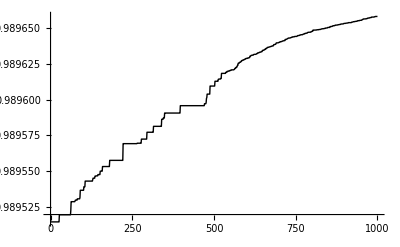

0.989658

```mathematica
fitP =ListLinePlot[fitness[[1;;Length[fitness]]],PlotStyle->Black,PlotRange->Automatic,ImageSize->400]
maxFit = Max[fitness]
```

## Robustness

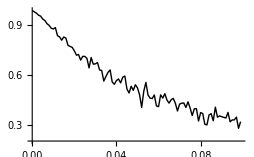

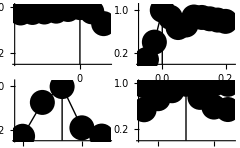

~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/readaptConstVel2.eps

```mathematica
(* Mutations *)
SetDirectory["/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_29__19_27_46"];
mutFitData=Import["Fitness.txt", "Table"];
fitData = mutFitData[[2;;-2]];
mutFit =fitData[[;;,1]];
grouped = Partition[mutFit,100];
means=Mean[Transpose[grouped]];
Length[means];
x=Range[0,0.099,0.001];
Length[x];
cm=72/2.54;
robPl=ListLinePlot[Transpose[{x,means}],PlotStyle->Black,AxesOrigin->{0,0.2},ImageSize->9cm]
(*Export[figExpPath<>"robustness.svg",robPl]*)

(* Shifts *)
(*opts={PlotMarkers->None,PlotStyle->Black,FillingStyle->{Black,AbsoluteThickness[10]},Filling->Axis,BaseStyle->{FontFamily->font}};*)
opts={PlotStyle->Black,BaseStyle->{FontFamily->font},Mesh->All,MeshStyle->{PointSize[0.045],Black},BaseStyle->{FontFamily->font}};
SetOptions[LinTicks,MajorTickLength->{0.03,0},MinorTickLength->{0.01,0},ShowMinorTicks->False];

shiftFit={0.896, 0.905,0.913,0.928,0.957,0.9896,0.916,0.71};
x=Range[-25,10,5];
shiftPl=ListLinePlot[Transpose[{x,shiftFit}],AxesOrigin->{-27.5,0},PlotRange->{{-27.5,12.5},{0,1.05*Max[shiftFit]}},opts,
Ticks->{LinTicks[-30,10],LinTicks[0,1,TickLabelStep->2,TickLabelStart->1]}, 
Epilog->{Line[{{0,0},{0,Max[shiftFit]}}]}];
shiftPl = Show[shiftPl];

(* Durations *)
durFits = {0.088,0.406,0.9896,0.8607,0.6723,0.719,0.865,0.857,0.832,0.809,0.785};
x=Range[-0.05,0.2,0.025];
durPl=ListLinePlot[Transpose[{x,durFits}],AxesOrigin->{-0.075,0},PlotRange->{{-0.075,0.225},{0,1.1*Max[durFits]}},opts,
Ticks->{LinTicks[-0.05,0.2,TickLabelStep->2,TickLabelStart->1],
LinTicks[0,1,TickLabelStep->2,TickLabelStart->1]}, 
Epilog->{Line[{{0,0},{0,Max[durFits]}}]}];

(* Amplitudes *)
ampFits = {0.0818,0.7,0.9896,0.2356,0.085};
x=Range[-10,10,5];
ampPl=ListLinePlot[Transpose[{x,ampFits}],AxesOrigin->{-12,0},PlotRange->{{-12,12},{0,1.1*Max[ampFits]}},opts,
Ticks->{LinTicks[-10,10],
LinTicks[0,1,TickLabelStep->2,TickLabelStart->1]}, 
Epilog->{Line[{{0,0},{0,Max[ampFits]}}]}];

(* Const velocity (changing duration and amplitude in proportion) *)
velFits = {0.54, 0.733,0.872,0.9896,0.756,0.587,0.544};
x=Range[-15,15,5];
velPl=ListLinePlot[Transpose[{x,velFits}],AxesOrigin->{-17,0},PlotRange->{{-17,17},{0,1.05*Max[velFits]}},opts,
Ticks->{LinTicks[-15,15,TickLabelStep->2,TickLabelStart->1],
LinTicks[0,1,TickLabelStep->2,TickLabelStart->1]}, 
Epilog->{Line[{{0,0},{0,Max[velFits]}}]}];

(* Readapted Const velocity (changing duration and amplitude in proportion) *)
revelFits = {0.959, 0.979,0.983,0.9896,0.988,0.987,0.984};
x=Range[-15,15,5];
revelPl=ListLinePlot[Transpose[{x,revelFits}],AxesOrigin->{-17,0},PlotRange->{{-17,17},{0,1.05*Max[velFits]}},PlotStyle->Red,opts,Ticks->{LinTicks[-15,15,TickLabelStep->2,TickLabelStart->1],
LinTicks[0,1,TickLabelStep->2,TickLabelStart->1]},
Epilog->{Line[{{0,0},{0,Max[revelFits]}}]} ];

general=Show[GraphicsGrid[{{shiftPl, durPl},{ampPl,Show[velPl,revelPl]}}], ImageSize->8.5cm]
(*readapt=Show[GraphicsGrid[{{shiftPl, durPl},{ampPl,velPl},{revelPl}}], ImageSize->8.5cm]*)
(*readapt = Show[revelPl, ImageSize->8.5cm]*)

(*Export[figExpPath<>"generalisation.eps",general]*)
Export[figExpPath<>"readaptConstVel2.eps",general]

SetDirectory[dirName];
```

## Config

```mathematica
dt = 0.001;
leadIn = 0.1;
leadOut = 0.2;
moveDuration = 0.3;
bestFitDelay = -0.0 / dt;
(*plotDuration = (moveDuration+leadOut/3) / dt;*)

trialDuration = leadIn+moveDuration+leadOut;
frontLead =0.1;
backLead = 1.0*leadOut;

numTrials=Round[numData/(trialDuration/dt)]

SetTrial[trial_]:=Module[{},
t0=2 +((leadIn-frontLead+ (trial*trialDuration))/dt);
tn=-2 +t0+(leadIn + moveDuration+backLead)/dt;
time=Range[tn-t0]*dt;
];

SetTrial[0];

padds={{20,40},{20,20}};
plotOptions = {PlotJoined->True, PlotRange->All, ImagePadding->padds};
graphicsWidth = 600;
font="Arial";
SetOptions[Plot,BaseStyle->{FontFamily->font}];
pad={{20,10},{15,10}};
```

4

## Functions

```mathematica
NtoI[name_]:=Position[varNames, name][[1,1]];
NtoD[name_, delay_:0]:=Table[data[[i,NtoI[name]]],{i,t0+delay,tn-1+delay}];
TimePlot[name_, options_, delay_:0,Scale_:1] := ListLinePlot[Transpose[{time,Scale*NtoD[name, delay]}], Join[options,plotOptions]];
TimePlotD[data_, options_, Scale_:1] := ListLinePlot[Transpose[{time,Scale*data}], Join[plotOptions,options]];

Maxima[x_,time_]:=Module[{max,peaks, times},
max = 1+Position[Differences[Sign[Differences[x]]],-2];
peaks = Extract[x, max];
times = Extract[time,max];
maxima = Transpose[{Flatten[times],peaks}];
maxima
]

Minima[x_,time_]:=Module[{min,peaks, times},
min = 1+Position[Differences[Sign[Differences[-x]]],-2];
peaks = -Extract[-x, min];
times = Extract[time,min];
minima = Transpose[{Flatten[times],peaks}];
minima
]

TimePlotMaxima[x_,time_, opt_:{}]:= ListPlot[Maxima[x,time],opt]
TimePlotMinima[x_,time_,opt_:{}]:= ListPlot[Minima[x,time],opt]
TimePlotOptima[x_, time_, opt1_:{},opt2_:{}]:=Module[{ma,mi},
ma=TimePlotMaxima[x, time,Join[{PlotStyle->Black},opt1]];
mi=TimePlotMinima[x,time,Join[{PlotStyle->Red},opt2]];
mami=Show[ma, mi];
mami
]

Shift[list_,del_]:=Module[{},
res=Drop[list,del];
res = If[del<0,
PadLeft[res,Length[list],res[[1]]],
PadRight[res,Length[list],res[[Length[res]]]]
]
];

(*l=Range[0,10]
l4=Shift[l,-2]*)
```

## All trajectories

28.3465

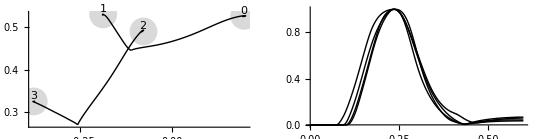

```mathematica
PlotTraj[trial_]:=Module[{},
SetTrial[trial];
x = NtoD["x"];
y = NtoD["y"];
elbX=NtoD["elbX"];
elbY=NtoD["elbY"];
desX=NtoD["desX"];
desY=NtoD["desY"];
positions=Transpose[{x,y}];
elbPositions=Transpose[{elbX,elbY}];
desPositions=Transpose[{desX,desY}];
cartesianPos=ListLinePlot[positions,plotOptions,PlotStyle->{Black},AxesOrigin->{Min[x],Min[y]}];
pos0=First[positions];
elb0=First[elbPositions];
posN=Last[positions];
elbN=Last[elbPositions];
startPos = Graphics[{PointSize[Large],Point[pos0]}];
elbStartPos = Graphics[{LightGray,PointSize[Large],Point[elb0]}];
desEndPos=Graphics[{LightGray,PointSize[0.05],Point[Last[desPositions]]}];
label=Graphics[Text[trial,Last[desPositions],{0,-2}]];
lower0=Graphics[{LightGray,Line[{elb0, pos0}]}];
upper0=Graphics[{LightGray,Line[{{0,0}, elb0}]}];
lowerN=Graphics[{LightGray,Line[{elbN, posN}]}];
upperN=Graphics[{LightGray,Line[{{0,0}, elbN}]}];
optimal = Graphics[{LightGray,Dashed,Line[{pos0, Last[desPositions]}]}];
Show[(*elbStartPos,lower0,upper0,*)(*lowerN,upperN, optimal,*) (*startPos,*)desEndPos,cartesianPos,label,BaseStyle->{FontFamily->font}]
]

TangVels[trial_] :=Module[{},
SetTrial[trial];
x = NtoD["x"];
y = NtoD["y"];
positions=Transpose[{x,y}];
vels= Map[Norm,Differences[positions]]/dt;
vels=PadRight[vels,Length[time],Last[vels]]
]

MaxTangVelPos[trial_]:=Module[{}, tangVels = TangVels[trial];Position[tangVels,Max[tangVels]][[1]] ]
maxVelPos = Flatten[Map[MaxTangVelPos,Range[0,numTrials-1,1]]];
velOff = maxVelPos-Min[maxVelPos];

PlotTangVels[trial_]:=Module[{},
vels=TangVels[trial];
(* Shift so peaks coincide *)
vels = Drop[vels,velOff[[trial+1]]];
vels=PadRight[vels,Length[vels]+velOff[[trial+1]], Last[vels]];
(* Scale to same peak *)
maxVel =Max[Map[Norm,vels]];
vels = vels / maxVel;
col = Black;(*If[trial < 2,Black,Gray];*)
ln = {};(*If[EvenQ[trial],{},Dashed];*)
tangVel=TimePlotD[vels,{PlotStyle->{col, ln},BaseStyle->{FontFamily->font}}]
];

PlotAngles[trial_,mmin_:50,mmax_:100]:=Module[{},
SetTrial[trial];
shdAng=NtoD["angleShoulder"]/Degree;
shdAngDes=NtoD["desShoulder"]/Degree;
shdAngCom =NtoD["comShoulder"]/Degree;
elbAng=NtoD["angleElbow"]/Degree;
elbAngDes=NtoD["desElbow"]/Degree;
elbAngCom =NtoD["comElbow"]/Degree;
min=Min[Min[elbAng],Min[shdAng]]*0.9;
max=Max[Max[elbAng],Max[shdAng]]*1.1;
shdPl= TimePlotD[shdAng,{PlotStyle->{Black}}];
shdPlDes= TimePlotD[shdAngDes,{PlotStyle->{LightGray,Thick}}];
shdPlCom= TimePlotD[shdAngCom,{PlotStyle->{Black,Dashed}}];
elbPl= TimePlotD[elbAng,{PlotStyle->{Black}}];
elbPlDes= TimePlotD[elbAngDes,{PlotStyle->{LightGray,Thick}}];
elbPlCom= TimePlotD[elbAngCom,{PlotStyle->{Black,Dashed}}];
Show[elbPlDes, shdPlDes,shdPl,elbPl,shdPlCom,elbPlCom,PlotRange->{{0,0.6},{min,max}},AxesOrigin->{0,min},BaseStyle->{FontFamily->font},ImagePadding->pad,
Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[mmin,mmax,TickLabelStep->2,TickLabelStart->1]} ]
];

PlotAngVels[trial_]:=Module[{},
SetTrial[trial];
shdVel=NtoD["velocityShoulder"]/Degree;
elbVel=NtoD["velocityElbow"]/Degree;
shdPl= TimePlotD[shdVel,{PlotStyle->{Black}}];
elbPl= TimePlotD[elbVel,{PlotStyle->{Black,Dashed}}];
Show[elbPl, shdPl]
];

(* Forces applied at joints, total is more or less acceleration *)
PlotTrqsElb[trial_,min_:-10,max_:10]:=Module[{},
SetTrial[trial];
itD = -NtoD["interactionElbow"] - NtoD["coriolisElbow"];
msD = NtoD["torqueElbow"];
totalD = msD +itD;
total = TimePlotD[totalD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}}];
trq= TimePlotD[msD,{PlotStyle->Black}];
it = TimePlotD[itD,{PlotStyle->{Black,Dashed}}];
mmin = 1.1*Min[{Min[itD],Min[msD],Min[totalD]}];
trqs = Show[total,trq, it,PlotRange->{{0,0.6},{mmin,Automatic}},AxesOrigin->{0,mmin},BaseStyle->{FontFamily->font},ImagePadding->pad,
Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[min,max,TickLabelStep->2,TickLabelStart->0]} ]
]

PlotAMNElb[trial_]:=Module[{},
SetTrial[trial];
aMNElbAgP =  TimePlot["reflexElbMNAg",{PlotStyle->Black}];
aMNElbAnP =  TimePlot["reflexElbMNAn",{PlotStyle->{Black,Dashed}}];
aMNElbPlot =Show[aMNElbAgP,aMNElbAnP ]
]

PlotAMNShd[trial_]:=Module[{},
SetTrial[trial];
aMNShdAgP =  TimePlot["reflexShdMNAg",{PlotStyle->Black}];
aMNShdAnP =  TimePlot["reflexShdMNAn",{PlotStyle->{Black,Dashed}}];
aMNShdPlot =Show[aMNShdAgP,aMNShdAnP ]
]

PlotTrqMElb[trial_]:=Module[{},
SetTrial[trial];
elbAgTrq = NtoD["ElbowFlexorTorque"];
elbAnTrq = NtoD["ElbowExtensorTorque"];
elbNetTrq = elbAgTrq - elbAnTrq;
max = Max[Max[Abs[elbAgTrq]],Max[Abs[elbAnTrq]],Max[Abs[elbNetTrq]]];
elbAgTorqueP = TimePlotD[elbAgTrq,{PlotStyle->{Black}, PlotRange->{Automatic,{-max*1.1, max*1.1}}}];
elbAnTorqueP = TimePlotD[elbAnTrq, {PlotStyle->{Black,Dashed}, PlotRange->{Automatic,{-max*1.1, max*1.1}}},-1];
elbNetTrqP = TimePlotD[elbNetTrq,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}, PlotRange->{Automatic,{-max*1.1, max*1.1}}}];
elbTrq = Show[elbNetTrqP,elbAgTorqueP,elbAnTorqueP, PlotRange->{Automatic,{-max, max}}]
]

PlotTrqMShd[trial_]:=Module[{},
SetTrial[trial];
shdAgTrq = NtoD["ShoulderFlexorTorque"];
shdAnTrq = NtoD["ShoulderExtensorTorque"];
shdNetTrq = shdAgTrq - shdAnTrq;
max = Max[Max[Abs[shdAgTrq]],Max[Abs[shdAnTrq]],Max[Abs[shdNetTrq]]];
shdAgTorqueP = TimePlotD[shdAgTrq,{PlotStyle->{Black}, PlotRange->{Automatic,{-max*1.1, max*1.1}},ImageSize->2cm}];
shdAnTorqueP = TimePlotD[shdAnTrq, {PlotStyle->{Black,Dashed}, PlotRange->{Automatic,{-max*1.1, max*1.1}}},-1];
shdNetTrqP = TimePlotD[shdNetTrq,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}, PlotRange->{Automatic,{-max*1.1, max*1.1}}}];
shdTrq = Show[shdNetTrqP,shdAgTorqueP,shdAnTorqueP,PlotRange->{Automatic,{-max, max}}]
]

PlotTrqsShd[trial_,min_:-10,max_:10]:=Module[{},
SetTrial[trial];
itD = -NtoD["interactionShoulder"] - NtoD["coriolisShoulder"];
msD = NtoD["torqueShoulder"];
totalD = msD +itD;
total = TimePlotD[totalD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent},ImageSize->22cm}];
trq= TimePlot["torqueShoulder",{PlotStyle->Black}];
it = TimePlotD[itD,{PlotStyle->{Black,Dashed}}];
mmin =1.1* Min[{Min[itD],Min[msD],Min[totalD]}];
mmax =1.1* Max[{Max[itD],Max[msD],Max[totalD]}];
trqs = Show[total,trq, it,PlotRange->{{0,0.6},{mmin,mmax}},AxesOrigin->{0,mmin},BaseStyle->{FontFamily->font},ImagePadding->pad,
Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[min,max,TickLabelStep->2,TickLabelStart->0,ShowMinorTicks->False]}]
]

trajsPl = Show[Table[PlotTraj[i],{i,0,numTrials-1}], Axes->True,AxesOrigin->{-0.45,0.25},ImagePadding->pad,AxesStyle->Thickness[.002]];


tangVelsPl=Show[Table[PlotTangVels[i],{i,0,numTrials-1}](*AspectRatio->1,*), ImagePadding->pad,AxesStyle->Thickness[.002]];

cm=72/2.54
angAndVel=Show[GraphicsRow[{trajsPl, tangVelsPl}],ImageSize->19cm]

(*Export[figExpPath<>"TrajStar4M2.eps",trajsPl]*)
(*Export[figExpPath<>"c1TrajAndVelNoIbIs.eps",angAndVel]*)

(*GraphicsGrid[Partition[Table[PlotAngles[i],{i,0,numTrials-1}],2],ImageSize->600]*)
(*GraphicsGrid[Partition[Table[PlotAngVels[i],{i,0,numTrials-1}],2],ImageSize->600]*)
(*GraphicsGrid[Partition[Table[PlotTrqsElb[i],{i,0,numTrials-1}],2],ImageSize->600]*)
tr1=0;
tr2=1;

(*mv12=GraphicsGrid[{{PlotAngles[tr1,40,90],PlotAngles[tr2,40,90]},{PlotTrqsElb[tr1,-2,2], PlotTrqsElb[tr2,-2,1]},{PlotTrqsShd[tr1,-12,12], PlotTrqsShd[tr2,-7,7]}},ImageSize->19cm,AxesStyle->Thickness[.002]]

mn12=GraphicsGrid[{{PlotAMNElb[tr1],PlotAMNShd[tr1],PlotAMNElb[tr2],PlotAMNShd[tr2]},
{PlotTrqMElb[tr1],PlotTrqMShd[tr1],PlotTrqMElb[tr2],PlotTrqMShd[tr2]}},ImageSize->22cm,AxesStyle->Thickness[.002]]

tr1=2;
tr2=3;
mv34=GraphicsGrid[{{PlotAngles[tr1],PlotAngles[tr2]},{PlotTrqsElb[tr1], PlotTrqsElb[tr2]},{PlotTrqsShd[tr1], PlotTrqsShd[tr2]}},ImageSize->19cm]


Export[figExpPath<>"c1AngleAndTorquesMv12.eps",mv12]
(*Export[figExpPath<>"c1AngleAndTorquesMv34.svg",mv34]
Export[figExpPath<>"aMN-Trq.pdf",mn12]*)
*)
```

```mathematica
TrajErr[trial_,del_:0] := Module[{},
SetTrial[trial];
(*Only actual movement, without leanIn or leadOut *)
tt0 = IntegerPart[leadIn/(2*dt)];
tt1 = -IntegerPart[leadOut/(2*dt)];
x = NtoD["x"][[tt0;;tt1]];
y = NtoD["y"][[tt0;;tt1]];
desX = Shift[NtoD["desX"][[tt0;;tt1]],del];
desY = Shift[NtoD["desY"][[tt0;;tt1]],del];
(*desX=NtoD["desX"][[tt0+del;;tt1+del]];*)
(*desY=NtoD["desY"][[tt0+del;;tt1+del]];*)
positions = Transpose[{x, y}];
desPositions = Transpose[{desX, desY}]; 
d=EuclideanDistance[desPositions[[1]],desPositions[[Length[desPositions]]] ];
se=MapThread[EuclideanDistance, {positions, desPositions}];
mse=Mean[se]*1000
];

maxShift=100;
TrajErrLag[trial_] := Module[{},
errs=Table[TrajErr[trial,d],{d,-maxShift,maxShift}];
Print[errs];
minErr=Min[errs];
minPos = Position[errs,minErr];
Print[-maxShift+minPos-1];
minErr
];

MaxRotVel[trial_] := Module[{},
SetTrial[trial];
elbVel = NtoD["velocityElbow"]/Degree;
shdVel = NtoD["velocityShoulder"]/Degree;
res = {Max[Abs[elbVel]], Max[Abs[shdVel]]}
]

(*t1=Table[TrajErr[i,0],{i,0,numTrials-1}]*)

t1l=Table[TrajErrLag[i],{i,0,numTrials-1}]
Mean[t1l]
t2=Table[Max[TangVels[i]],{i,0,numTrials-1}]
t3=Table[MaxRotVel[i],{i,0,numTrials-1}]
```

{69.8509,69.1405,68.4301,67.7198,67.0094,66.299,65.5886,64.8783,64.1679,63.4575,62.7471,62.0367,61.3264,60.616,59.9056,59.1952,58.4849,57.7745,57.0642,56.3538,55.6435,54.9331,54.2228,53.5124,52.8021,52.0918,51.3815,50.6712,49.961,49.2507,48.5405,47.8302,47.12,46.4098,45.6996,44.9895,44.2793,43.5692,42.8591,42.1491,41.439,40.729,40.019,39.3091,38.5992,37.8893,37.1795,36.4697,35.76,35.0503,34.3407,33.6311,32.9216,32.2121,31.5028,30.7935,30.0843,29.3752,28.6662,27.9573,27.2485,26.5399,25.8314,25.1231,24.4149,23.707,22.9993,22.2918,21.5846,20.8778,20.1714,19.4654,18.76,18.0553,17.3514,16.6487,15.9474,15.2483,14.5525,13.8613,13.1765,12.4989,11.8289,11.1667,10.5128,9.86751,9.23154,8.60576,7.99129,7.38957,6.80248,6.23253,5.68317,5.1593,4.66827,4.22176,3.8399,3.56296,3.49183,3.58747,3.81359,4.2096,4.72764,5.30711,5.92367,6.56448,7.22175,7.89052,8.56757,9.25075,9.93857,10.63,11.3242,12.0207,12.7191,13.4189,14.1201,14.8222,15.5253,16.2292,16.9337,17.6388,18.3444,19.0505,19.7569,20.4637,21.1708,21.8782,22.5859,23.2937,24.0018,24.71,25.4184,26.127,26.8357,27.5446,28.2535,28.9626,29.6718,30.381,31.0904,31.7998,32.5093,33.2189,33.9285,34.6382,35.348,36.0578,36.7677,37.4776,38.1875,38.8975,39.6075,40.3176,41.0277,41.7378,42.448,43.1581,43.8682,44.5784,45.2885,45.9985,46.7085,47.4184,48.1282,48.8379,49.5475,50.257,50.9662,51.6753,52.3841,53.0927,53.801,54.509,55.2167,55.924,56.6309,57.3374,58.0435,58.7491,59.4541,60.1587,60.8626,61.5659,62.2686,62.9705,63.6718,64.3723,65.0719,65.7708,66.4687,67.1657,67.8618,68.5569,69.2509,69.9438,70.6356,71.3262,72.0156,72.7038,73.3906}

{{-2}}

{24.9666,24.718,24.4694,24.2209,23.9724,23.7238,23.4753,23.2268,22.9783,22.7297,22.4812,22.2327,21.9842,21.7357,21.4871,21.2386,20.9901,20.7416,20.493,20.2445,19.996,19.7474,19.4989,19.2503,19.0018,18.7532,18.5047,18.2561,18.0075,17.759,17.5104,17.2619,17.0133,16.7647,16.5162,16.2676,16.0191,15.7706,15.5221,15.2736,15.0251,14.7767,14.5283,14.2799,14.0315,13.7832,13.535,13.2868,13.0387,12.7907,12.5427,12.2949,12.0472,11.7996,11.5522,11.305,11.058,10.8113,10.5649,10.3188,10.0732,9.8282,9.58388,9.34057,9.0989,8.85845,8.61911,8.38082,8.14358,7.90738,7.67225,7.43821,7.20529,6.97354,6.74301,6.51375,6.28582,6.05932,5.83431,5.61089,5.38918,5.16929,4.95137,4.73559,4.52213,4.31122,4.10313,3.89817,3.69673,3.49928,3.30643,3.11894,2.93779,2.76426,2.59994,2.44672,2.30667,2.18229,2.07664,1.99369,1.939,1.92106,1.95568,2.08288,2.26595,2.47097,2.68832,2.91353,3.14415,3.3787,3.61619,3.85596,4.09752,4.34054,4.58475,4.82995,5.07598,5.32271,5.57004,5.8179,6.06621,6.31491,6.56396,6.81333,7.06296,7.31285,7.56295,7.81325,8.06373,8.31437,8.56517,8.81609,9.06714,9.3183,9.56957,9.82093,10.0724,10.3239,10.5755,10.8272,11.0789,11.3307,11.5826,11.8345,12.0864,12.3384,12.5905,12.8425,13.0947,13.3468,13.599,13.8512,14.1035,14.3557,14.608,14.8603,15.1127,15.365,15.6173,15.8697,16.122,16.3744,16.6267,16.879,17.1313,17.3836,17.6358,17.8879,18.14,18.3921,18.644,18.8959,19.1477,19.3994,19.651,19.9024,20.1537,20.4049,20.6559,20.9067,21.1574,21.4078,21.6581,21.9081,22.1579,22.4075,22.6568,22.9059,23.1546,23.4031,23.6512,23.899,24.1465,24.3936,24.6403,24.8867,25.1327,25.3782,25.6233,25.868,26.1122}

{{1}}

{70.3659,69.7344,69.1029,68.4713,67.8398,67.2083,66.5768,65.9452,65.3137,64.6822,64.0506,63.4191,62.7875,62.156,61.5244,60.8929,60.2613,59.6298,58.9982,58.3666,57.7351,57.1035,56.4719,55.8404,55.2088,54.5772,53.9457,53.3141,52.6825,52.051,51.4194,50.7878,50.1563,49.5247,48.8931,48.2616,47.63,46.9985,46.3669,45.7354,45.1038,44.4723,43.8408,43.2092,42.5777,41.9462,41.3147,40.6832,40.0517,39.4203,38.7888,38.1574,37.526,36.8946,36.2632,35.6318,35.0004,34.3691,33.7378,33.1065,32.4753,31.8441,31.2129,30.5818,29.9506,29.3196,28.6886,28.0576,27.4267,26.7959,26.1651,25.5343,24.9037,24.2732,23.6427,23.0123,22.3821,21.7519,21.1219,20.492,19.8623,19.2328,18.6034,17.9743,17.3454,16.7168,16.0884,15.4604,14.8328,14.2056,13.5789,12.9528,12.3274,11.7027,11.079,10.4563,9.835,9.21532,8.5977,7.98274,7.37138,6.76536,6.16799,5.58461,5.02244,4.49044,3.99929,3.56126,3.18969,2.89947,2.713,2.68153,2.87972,3.23344,3.67789,4.18179,4.72455,5.29255,5.87717,6.473,7.07665,7.68593,8.29936,8.91595,9.53498,10.1559,10.7785,11.4022,12.027,12.6527,13.2791,13.9062,14.5337,15.1617,15.7902,16.4189,17.048,17.6773,18.3069,18.9367,19.5667,20.1968,20.8272,21.4576,22.0882,22.7188,23.3496,23.9805,24.6115,25.2425,25.8736,26.5048,27.136,27.7673,28.3987,29.03,29.6614,30.2929,30.9243,31.5557,32.1871,32.8185,33.4499,34.0812,34.7124,35.3435,35.9745,36.6053,37.2361,37.8666,38.4969,39.1271,39.7569,40.3866,41.0159,41.6449,42.2735,42.9018,43.5297,44.1572,44.7842,45.4107,46.0366,46.6621,47.2869,47.9112,48.5347,49.1576,49.7798,50.4012,51.0219,51.6417,52.2607,52.8787,53.4959,54.112,54.7272,55.3413,55.9543,56.5662,57.177}

{{11}}

{31.2824,30.9903,30.6982,30.406,30.1139,29.8218,29.5297,29.2376,28.9455,28.6534,28.3613,28.0692,27.7771,27.485,27.1929,26.9008,26.6087,26.3166,26.0245,25.7325,25.4404,25.1483,24.8562,24.5641,24.272,23.98,23.6879,23.3958,23.1037,22.8117,22.5196,22.2275,21.9354,21.6434,21.3513,21.0593,20.7672,20.4751,20.1831,19.891,19.599,19.3069,19.0149,18.7229,18.4308,18.1388,17.8468,17.5548,17.2628,16.9708,16.6788,16.3868,16.0949,15.8029,15.511,15.219,14.9271,14.6352,14.3433,14.0515,13.7596,13.4678,13.176,12.8842,12.5925,12.3008,12.0091,11.7175,11.4259,11.1343,10.8428,10.5514,10.26,9.96873,9.6775,9.38636,9.09532,8.80439,8.51358,8.22292,7.93241,7.64208,7.35197,7.0621,6.77252,6.48329,6.19446,5.90613,5.61841,5.33145,5.04546,4.76071,4.4776,4.19663,3.91849,3.644,3.37414,3.10994,2.85256,2.60334,2.36398,2.13687,1.92571,1.73606,1.57466,1.45354,1.39476,1.43378,1.58032,1.79273,2.03738,2.29869,2.56943,2.84598,3.12634,3.40932,3.69418,3.98044,4.26776,4.55591,4.84471,5.13405,5.42381,5.71394,6.00437,6.29504,6.58594,6.87702,7.16826,7.45964,7.75115,8.04276,8.33446,8.62625,8.91812,9.21005,9.50205,9.7941,10.0862,10.3783,10.6705,10.9627,11.255,11.5473,11.8396,12.132,12.4243,12.7167,13.0091,13.3016,13.594,13.8865,14.179,14.4715,14.764,15.0565,15.349,15.6415,15.9341,16.2266,16.5191,16.8116,17.104,17.3965,17.6889,17.9812,18.2735,18.5657,18.8579,19.1499,19.4419,19.7338,20.0255,20.3172,20.6087,20.9,21.1912,21.4822,21.773,22.0637,22.3541,22.6443,22.9342,23.2239,23.5133,23.8024,24.0913,24.3798,24.668,24.9558,25.2433,25.5304,25.817,26.1033,26.3892,26.6746,26.9595,27.2439,27.5279,27.8113,28.0942}

{{6}}

{3.49183,1.92106,2.68153,1.39476}

2.3723

{1.91779,0.729801,1.85244,0.822652}

{{277.406,186.886},{194.072,122.391},{250.736,183.946},{185.392,125.304}}

```mathematica
Mean[{1.48414,1.87025,2.16494,0.974298,8.99603,2.78482,1.59068,14.06928405}]
```

4.24181

## Draw arm kinematics

```mathematica
SetTrial[0];

(* Joint trajectories *)
elbAng=NtoD["angleElbow"]/Degree;
elbDes = NtoD["desElbow"]/Degree;
elbCom = NtoD["comElbow"]/Degree;
angleElb =TimePlotD[elbAng,{PlotStyle->{Black}, AxesLabel->{"time","angle"}}];
desAngleElb = TimePlotD[elbDes,{PlotStyle->{Black,Dashed}, AxesLabel->{"time","angle"}}];
comAngleElb = TimePlotD[elbCom,{PlotStyle->{Gray}, AxesLabel->{"time","angle"}}];

shdAng=NtoD["angleShoulder"]/Degree;
shdDes = NtoD["desShoulder"]/Degree;
shdCom = NtoD["comShoulder"]/Degree;
angleShd= TimePlotD[shdAng,{PlotStyle->{Black}}];
desAngleShd = TimePlotD[shdDes,{PlotStyle->{Black,Dashed}, AxesLabel->{"time","angle"}}];
comAngleShd = TimePlotD[shdCom,{PlotStyle->{Gray}, AxesLabel->{"time","angle"}}];
elbow = Show[angleElb, desAngleElb, comAngleElb];
shoulder = Show[angleShd, desAngleShd, comAngleShd];

(* Calculate derivatives *)
accScale = 10;

velElb= TimePlot["velocityElbow",{PlotStyle->{Black}, AxesLabel->{"time","velocity"}}];
desVelElbD = Differences[NtoD["desElbow", bestFitDelay]]/dt;
desVelElbD = PadRight[desVelElbD,Length[time],Last[desVelElbD]];
desVelElb = TimePlotD[desVelElbD,{PlotStyle->{Black,Dashed}}];
desAccElbD = Differences[desVelElbD]/dt/accScale;
desAccElbD = PadRight[desAccElbD,Length[time],Last[desAccElbD]];
desAccElbD = MovingAverage[desAccElbD,3];
desAccElbD = PadRight[desAccElbD,Length[time],Last[desAccElbD]];
desAccElb = TimePlotD[desAccElbD,{PlotStyle->{Gray}}];

velShd= TimePlot["velocityShoulder",{PlotStyle->{Black}}];
desVelShdD = Differences[NtoD["desShoulder", bestFitDelay]]/dt;
desVelShdD = Append[desVelShdD,desVelShdD[[Length[desVelShdD]]]];
desVelShd = TimePlotD[desVelShdD,{PlotStyle->{Black,Dashed}}];
desAccShdD = Differences[desVelShdD]/dt/accScale;
desAccShdD = PadRight[desAccShdD,Length[time],Last[desAccShdD]];
desAccShdD = MovingAverage[desAccShdD,3];
desAccShdD = PadRight[desAccShdD,Length[time],Last[desAccShdD]];
desAccShd = TimePlotD[desAccShdD,{PlotStyle->{Gray}}];

velsElb = Show[velElb, desVelElb, desAccElb];
velsShd = Show[velShd, desVelShd, desAccShd];
vels = Show[velElb,velShd];

(* Forces applied at joints, total is more or less acceleration *)
itElbD = -NtoD["interactionElbow"] - NtoD["coriolisElbow"];
msElbD = NtoD["torqueElbow"];
totalElbD = msElbD +itElbD;
totalElb = TimePlotD[totalElbD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}, AxesLabel->{"time","forceElb"}}];
trqElb= TimePlot["torqueElbow",{PlotStyle->Black}];
itElb = TimePlotD[itElbD,{PlotStyle->{Black,Dashed}}];
(*opttotalP = TimePlotOptima[totalElbD, time];
optitP = TimePlotOptima[itElbD, time];
optmsP = TimePlotOptima[msElbD, time];*)
trqsElb = Show[totalElb,trqElb, itElb(*, opttotalP,optitP, optmsP*)];

(*Maxima[totalElbD,time][[1]]*)

itShdD = -NtoD["interactionShoulder"] - NtoD["coriolisShoulder"];
totalShdD = NtoD["torqueShoulder"]+itShdD;
totalShd = TimePlotD[totalShdD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent},AxesLabel->{"time","forceShd"}}];
trqShd= TimePlot["torqueShoulder",{PlotStyle->Black}];
itShd = TimePlotD[itShdD,{PlotStyle->{Black,Dashed}}];
trqsShd = Show[totalShd,trqShd, itShd];


(* Effector space trajectories, i.e. cartesian position *)
xPos = TimePlot["x",{PlotStyle->{Black}, AxesLabel->{"time","x,y"}}];
desX = TimePlot["desX",{PlotStyle->{Black, Dashed}, AxesLabel->{"time","x,y"}}, bestFitDelay];
comX = TimePlot["comX",{PlotStyle->{Gray}, AxesLabel->{"time","x,y"}}];
yPos = TimePlot["y",{PlotStyle->{Black}}];
desY = TimePlot["desY",{PlotStyle->{Black, Dashed}, AxesLabel->{"time","x,y"}}, bestFitDelay];
comY = TimePlot["comY",{PlotStyle->{Gray}, AxesLabel->{"time","x,y"}}];
pos = Show[xPos,yPos, desX, desY];
posX = Show[xPos, desX, comX];
posY = Show[yPos, desY, comY];

(* XY plot *)
x = NtoD["x"];
y = NtoD["y"];
positions=Transpose[{x,y}];
cartesianPos=ListLinePlot[positions,plotOptions,PlotStyle->Black,AxesOrigin->{Min[x],Min[y]}, AxesLabel->{"x","y"}];
startPos = Graphics[{PointSize[Large],Point[First[positions]]}];
desX = Shift[NtoD["desX"],-50];
desY = Shift[NtoD["desY"],-50];
desPos = Transpose[{desX,desY}];
desCartPos = ListLinePlot[desPos,plotOptions,PlotStyle->{Black,Dashed},AxesOrigin->{Min[x],Min[y]}, AxesLabel->{"x","y"}];
sample=Table[{positions[[i]],desPos[[i]]},{i,50,Length[desPos],10}];
paral=Graphics[{Gray,Line[sample]}];
xyPos = Show[cartesianPos,desCartPos,paral];

(* Calculate tangential velocity *)
vels= Map[Norm,Differences[positions]]/dt;
vels=PadRight[vels,Length[time],Last[vels]];
tangVel=TimePlotD[vels,{PlotStyle->{Black},AxesLabel->{"time","vel"}}];
desVels = Map[Norm,Differences[desPos]]/dt;
desVels = PadRight[desVels,Length[time],Last[desVels]];
tangDesVel = TimePlotD[desVels,{PlotStyle->{Black,Dashed},AxesLabel->{"time","vel"}}];
cartVels = Show[tangVel,tangDesVel]; 

(*(gg=GraphicsGrid[{{pos,angles,vels},{accs,trqsElb, trqsShd}}, ImageSize->{1200}]*)
armPlots=GraphicsGrid[{{xyPos, cartVels},{posX, posY},{elbow, shoulder}, {velsElb,velsShd}, {trqsElb,trqsShd}}, ImageSize->graphicsWidth];

posVelPl = GraphicsRow[{
Show[xyPos,Ticks->{LinTicks[-0.15,0.2,TickLabelStep->2,TickLabelStart->1],
LinTicks[0.45,0.53,TickLabelStep->2,TickLabelStart->1]},AxesLabel->{}], 
Show[cartVels,Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[0,2,TickLabelStep->2,TickLabelStart->1]},AxesLabel->{}]
}(*,ImageSize->19cm*)]

(*Export["export.pdf", gg, "pdf"]*)
(*Export[figExpPath<>"Ablation1.eps",posVelPl]*)
```

-Graphics-

## Reflex plots

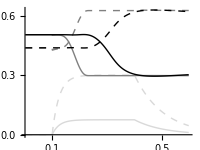

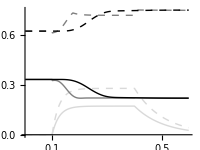

```mathematica
SetTrial[0];

(* Input: desired contraction modified by intersegmental input *)
(*desContrElbAgP =  TimePlot["reflexElbDesContractionAg",{PlotStyle->Red, AxesLabel->{"time","DesContr"}}];
desContrElbAnP =  TimePlot["reflexElbDesContractionAn",{PlotStyle->{Red,Dashed}}];*)
(*comContrElbAgP =  TimePlot["reflexElbComContractionAg",{PlotStyle->{Gray}}];
comContrElbAnP =  TimePlot["reflexElbComContractionAn",{PlotStyle->{Gray,Dashed}}];*)
comContrElbAg = 1-( 1-NtoD["reflexElbComContractionAg"]+NtoD["reflexElbOpenLoopAg"]);
comContrElbAn =  1-( 1-NtoD["reflexElbComContractionAn"]+NtoD["reflexElbOpenLoopAn"]);
comContrElbAgP =  TimePlotD[comContrElbAg,{PlotStyle->{Gray}}];
comContrElbAnP =  TimePlotD[comContrElbAn,{PlotStyle->{Gray,Dashed}}];
comOLElbAgP= TimePlot["reflexElbOpenLoopAg",{PlotStyle->{LightGray}}];
comOLElbAnP= TimePlot["reflexElbOpenLoopAn",{PlotStyle->{LightGray,Dashed}}];
actContrElbAgP =  TimePlot["reflexElbActContractionAg",{PlotStyle->{Black}}];
actContrElbAnP =  TimePlot["reflexElbActContractionAn",{PlotStyle->{Black,Dashed}}];
desContrElbPlot =Show[comOLElbAgP,comOLElbAnP,comContrElbAgP,comContrElbAnP,actContrElbAgP,actContrElbAnP,ImageSize->200,Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[0,0.7,TickLabelStep->1,TickLabelStart->0,ShowMinorTicks->False]},AspectRatio->0.75]

(*desContrShdAgP =  TimePlot["reflexShdDesContractionAg",{PlotStyle->Black, AxesLabel->{"time","DesContr"}}];
desContrShdAnP =  TimePlot["reflexShdDesContractionAn",{PlotStyle->{Black,Dashed}}];
comContrShdAgP =  TimePlot["reflexShdComContractionAg",{PlotStyle->{Gray}}];
comContrShdAnP =  TimePlot["reflexShdComContractionAn",{PlotStyle->{Gray,Dashed}}];*)
comContrShdAg = 1-( 1-NtoD["reflexShdComContractionAg"]+NtoD["reflexShdOpenLoopAg"]);
comContrShdAn =  1-( 1-NtoD["reflexShdComContractionAn"]+NtoD["reflexShdOpenLoopAn"]);
comContrShdAgP =  TimePlotD[comContrShdAg,{PlotStyle->{Gray}}];
comContrShdAnP =  TimePlotD[comContrShdAn,{PlotStyle->{Gray,Dashed}}];
comOLShdAgP= TimePlot["reflexShdOpenLoopAg",{PlotStyle->{LightGray}}];
comOLShdAnP= TimePlot["reflexShdOpenLoopAn",{PlotStyle->{LightGray,Dashed}}];
actContrShdAgP =  TimePlot["reflexShdActContractionAg",{PlotStyle->{Black}}];
actContrShdAnP =  TimePlot["reflexShdActContractionAn",{PlotStyle->{Black,Dashed}}];
desContrShdPlot =Show[comOLShdAgP,comOLShdAnP,comContrShdAgP,comContrShdAnP,actContrShdAgP,actContrShdAnP,ImageSize->200,Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[0,0.7,TickLabelStep->1,TickLabelStart->0,ShowMinorTicks->False]},AspectRatio->0.75]

(* Overall output: alpha MN *)
aMNElbAgP =  TimePlot["reflexElbMNAg",{PlotStyle->Black, AxesLabel->{"time","aMN"}}];
aMNElbAnP =  TimePlot["reflexElbMNAn",{PlotStyle->{Black,Dashed}}];
aMNElbPlot =Show[aMNElbAgP,aMNElbAnP ];

aMNShdAgP =  TimePlot["reflexShdMNAg",{PlotStyle->Black, AxesLabel->{"time","aMN"}}];
aMNShdAnP =  TimePlot["reflexShdMNAn",{PlotStyle->{Black,Dashed}}];
aMNShdPlot =Show[aMNShdAgP,aMNShdAnP ];

(* Open loop activation *)
oplpElbAgP =  TimePlot["reflexElbOpenLoopAg",{PlotStyle->Black, AxesLabel->{"time","openLoop"}}];
oplpElbAnP =  TimePlot["reflexElbOpenLoopAn",{PlotStyle->{Black,Dashed}}];
oplpElbPlot=Show[oplpElbAgP,oplpElbAnP ];

oplpShdAgP =  TimePlot["reflexShdOpenLoopAg",{PlotStyle->Black, AxesLabel->{"time","openLoop"}}];
oplpShdAnP =  TimePlot["reflexShdOpenLoopAn",{PlotStyle->{Black,Dashed}}];
oplpShdPlot=Show[oplpShdAgP,oplpShdAnP ];

(* Spindles *)
spElbAgP =  TimePlot["reflexElbSpResAg",{PlotStyle->Black, AxesLabel->{"time","spindle"}}];
spElbAnP =  TimePlot["reflexElbSpResAn",{PlotStyle->{Black,Dashed}}];
spindleElbPlot =Show[spElbAgP,spElbAnP ];

spShdAgP =  TimePlot["reflexShdSpResAg",{PlotStyle->Black, AxesLabel->{"time","spindle"}}];
spShdAnP =  TimePlot["reflexShdSpResAn",{PlotStyle->{Black,Dashed}}];
spindleShdPlot =Show[spShdAgP,spShdAnP ];

(* Spindles components*)
spElbAgPosP =  TimePlot["reflexElbPosResAg",{PlotStyle->Black, AxesLabel->{"time","spCmpAg"}}];
spElbAgVelP =  TimePlot["reflexElbVelResAg",{PlotStyle->{Black,Dashed}}];
spElbAgDmpP =  TimePlot["reflexElbDmpResAg",{PlotStyle->{Black,Dotted}}];
spShdAgPosP =  TimePlot["reflexShdPosResAg",{PlotStyle->Black}];
spShdAgVelP =  TimePlot["reflexShdVelResAg",{PlotStyle->{Black,Dashed}}];
spShdAgDmpP =  TimePlot["reflexShdDmpResAg",{PlotStyle->{Black,Dotted}}];
spCmpElbAgPlot =Show[spElbAgPosP,spElbAgVelP,spElbAgDmpP];
spCmpShdAgPlot =Show[spShdAgPosP,spShdAgVelP,spShdAgDmpP];

spElbAnPosP =  TimePlot["reflexElbPosResAn",{PlotStyle->Black, AxesLabel->{"time","spCmpAn"}}];
spElbAnVelP =  TimePlot["reflexElbVelResAn",{PlotStyle->{Black,Dashed}}];spElbAnDmpP =  TimePlot["reflexElbDmpResAn",{PlotStyle->{Black,Dotted}}];
spShdAnPosP =  TimePlot["reflexShdPosResAn",{PlotStyle->Black}];
spShdAnVelP =  TimePlot["reflexShdVelResAn",{PlotStyle->{Black,Dashed}}];spShdAnDmpP =  TimePlot["reflexShdDmpResAn",{PlotStyle->{Black,Dotted}}];
spCmpElbAnPlot =Show[spElbAnPosP,spElbAnVelP,spElbAnDmpP];
spCmpShdAnPlot =Show[spShdAnPosP,spShdAnVelP,spShdAnDmpP];

(* IaIn activation *)
iainElbAgP =  TimePlot["reflexElbIaInAg",{PlotStyle->Black, AxesLabel->{"time","IaIn"}}];
iainElbAnP =  TimePlot["reflexElbIaInAn",{PlotStyle->{Black,Dashed}}];
iainElbPlot=Show[iainElbAgP,iainElbAnP ];
iainShdAgP =  TimePlot["reflexShdIaInAg",{PlotStyle->Black, AxesLabel->{"time","IaIn"}}];
iainShdAnP =  TimePlot["reflexShdIaInAn",{PlotStyle->{Black,Dashed}}];
iainShdPlot=Show[iainShdAgP,iainShdAnP ];

(* IbIn activation *)
ibinElbAgP =  TimePlot["reflexElbIbInAg",{PlotStyle->Black, AxesLabel->{"time","IbIn"}}];
ibinElbAnP =  TimePlot["reflexElbIbInAn",{PlotStyle->{Black,Dashed}}];
ibinElbPlot=Show[ibinElbAgP,ibinElbAnP ];
ibinShdAgP =  TimePlot["reflexShdIbInAg",{PlotStyle->Black, AxesLabel->{"time","IbIn"}}];
ibinShdAnP =  TimePlot["reflexShdIbInAn",{PlotStyle->{Black,Dashed}}];
ibinShdPlot=Show[ibinShdAgP,ibinShdAnP ];

(* Rn activation *)
rnElbAgP =  TimePlot["reflexElbRenshawAg",{PlotStyle->Black, AxesLabel->{"time","Rn"}}];
rnElbAnP =  TimePlot["reflexElbRenshawAn",{PlotStyle->{Black,Dashed}}];
rnElbPlot=Show[rnElbAgP,rnElbAnP ];
rnShdAgP =  TimePlot["reflexShdRenshawAg",{PlotStyle->Black, AxesLabel->{"time","Rn"}}];
rnShdAnP =  TimePlot["reflexShdRenshawAn",{PlotStyle->{Black,Dashed}}];
rnShdPlot=Show[rnShdAgP,rnShdAnP ];

reflexPlots = GraphicsGrid[{{desContrElbPlot, desContrShdPlot},{aMNElbPlot, aMNShdPlot}, {oplpElbPlot,oplpShdPlot},{spindleElbPlot,spindleShdPlot},{spCmpElbAgPlot,spCmpShdAgPlot},{spCmpElbAnPlot,spCmpShdAnPlot},{iainElbPlot,iainShdPlot},{ibinElbPlot,ibinShdPlot},{rnElbPlot, rnShdPlot}}, ImageSize->graphicsWidth];
```

## Muscle Plots

```mathematica
elbAgActP = TimePlot["ElbowFlexorAct",{PlotStyle->{Black},AxesLabel->{"time","Act"}}];
elbAnActP = TimePlot["ElbowExtensorAct", {PlotStyle->{Black,Dashed}}];
elbAct = Show[elbAgActP, elbAnActP];

shdAgActP = TimePlot["ShoulderFlexorAct",{PlotStyle->{Black}}];
shdAnActP = TimePlot["ShoulderExtensorAct", {PlotStyle->{Black,Dashed}}];
shdAct = Show[shdAgActP, shdAnActP];


elbAgFrcP = TimePlot["ElbowFlexorForce",{PlotStyle->{Black},AxesLabel->{"time","Force"}}];
elbAnFrcP = TimePlot["ElbowExtensorForce", {PlotStyle->{Black,Dashed}}];
elbFrcTotal = Show[elbAgFrcP, elbAnFrcP];

shdAgFrcP = TimePlot["ShoulderFlexorForce",{PlotStyle->{Black}}];
shdAnFrcP = TimePlot["ShoulderExtensorForce", {PlotStyle->{Black,Dashed}}];
shdFrcTotal = Show[shdAgFrcP, shdAnFrcP];


elbAgLengthP = TimePlot["ElbowFlexorLengthNorm",{PlotStyle->{Black},AxesLabel->{"time","Length"}}];
elbAnLengthP = TimePlot["ElbowExtensorLengthNorm", {PlotStyle->{Black,Dashed}}];
elbAgVelP = TimePlot["ElbowFlexorVelocityNorm",{PlotStyle->{Gray}}];
elbAnVelP = TimePlot["ElbowExtensorVelocityNorm", {PlotStyle->{Gray,Dashed}}];
elbKin = Show[elbAgLengthP,elbAnLengthP(*,elbAgVelP,elbAnVelP*)];

shdAgLengthP = TimePlot["ShoulderFlexorLengthNorm",{PlotStyle->{Black}}];
shdAnLengthP = TimePlot["ShoulderExtensorLengthNorm", {PlotStyle->{Black,Dashed}}];
shdAgVelP = TimePlot["ShoulderFlexorVelocityNorm",{PlotStyle->{Gray}}];
shdAnVelP = TimePlot["ShoulderExtensorVelocityNorm", {PlotStyle->{Gray,Dashed}}];
shdKin = Show[shdAgLengthP,shdAnLengthP(*,shdAgVelP,shdAnVelP*)];

elbAgActFrcP = TimePlot["ElbowFlexorFrcAct", {PlotStyle->{Black},AxesLabel->{"time","FrcCmp"}}];
elbAnActFrcP = TimePlot["ElbowExtensorFrcAct", {PlotStyle->{Black,Dashed}}];
elbAgVelFrcP = TimePlot["ElbowFlexorFrcVel", {PlotStyle->{Gray},AxesLabel->{"time","FrcCmp"}}];
elbAnVelFrcP = TimePlot["ElbowExtensorFrcVel", {PlotStyle->{Gray,Dashed}}];
elbAgPsvFrcP = TimePlot["ElbowFlexorFrcPsv", {PlotStyle->{LightGray},AxesLabel->{"time","FrcCmp"}}];
elbAnPsvFrcP = TimePlot["ElbowExtensorFrcPsv", {PlotStyle->{LightGray,Dashed}}];
elbFrc = Show[elbAgActFrcP, elbAnActFrcP,elbAgVelFrcP,elbAnVelFrcP(*,elbAgPsvFrcP,elbAnPsvFrcP*)];

shdAgActFrcP = TimePlot["ShoulderFlexorFrcAct", {PlotStyle->{Black}}];
shdAnActFrcP = TimePlot["ShoulderExtensorFrcAct", {PlotStyle->{Black,Dashed}}];
shdAgVelFrcP = TimePlot["ShoulderFlexorFrcVel", {PlotStyle->{Gray}}];
shdAnVelFrcP = TimePlot["ShoulderExtensorFrcVel", {PlotStyle->{Gray,Dashed}}];
shdAgPsvFrcP = TimePlot["ShoulderFlexorFrcPsv", {PlotStyle->{LightGray}}];
shdAnPsvFrcP = TimePlot["ShoulderExtensorFrcPsv", {PlotStyle->{LightGray,Dashed}}];
shdFrc = Show[shdAgActFrcP, shdAnActFrcP,shdAgVelFrcP,shdAnVelFrcP(*,shdAgPsvFrcP,shdAnPsvFrcP*)];


shdNetTrq = NtoD["ShoulderFlexorTorque", bestFitDelay] - NtoD["ShoulderExtensorTorque"];
elbNetTrq = NtoD["ElbowFlexorTorque", bestFitDelay] - NtoD["ElbowExtensorTorque"];
elbNetTrqP = TimePlotD[elbNetTrq,{}];
shdNetTrqP = TimePlotD[shdNetTrq,{}];

elbAgMaP = TimePlot["ElbowFlexorMomentArm",{PlotStyle->{Black},AxesLabel->{"time","MA"}}];
elbAnMaP = TimePlot["ElbowExtensorMomentArm", {PlotStyle->{Black,Dashed}}];
elbAgTorqueP = TimePlot["ElbowFlexorTorque",{PlotStyle->{Black},AxesLabel->{"time","Torque"}}];
elbAnTorqueP = TimePlot["ElbowExtensorTorque", {PlotStyle->{Black,Dashed}}];
elbTrq = Show[elbAgTorqueP,elbAnTorqueP, elbNetTrqP];
elbMa = Show[elbAgMaP, elbAnMaP];

shdAgMaP = TimePlot["ShoulderFlexorMomentArm",{PlotStyle->{Black}}];
shdAnMaP = TimePlot["ShoulderExtensorMomentArm", {PlotStyle->{Black,Dashed}}];
shdAgTorqueP = TimePlot["ShoulderFlexorTorque",{PlotStyle->{Black}}];
shdAnTorqueP = TimePlot["ShoulderExtensorTorque", {PlotStyle->{Black,Dashed}}];
shdTrq = Show[shdAgTorqueP,shdAnTorqueP, shdNetTrqP];
shdMa = Show[shdAgMaP, shdAnMaP];

musclePlots = GraphicsGrid[{{elbAct,shdAct},{elbFrcTotal,shdFrcTotal},{elbKin,shdKin},{elbFrc,shdFrc},{elbMa,shdMa},{elbTrq,shdTrq}},ImageSize->graphicsWidth];
```

## Phase Space plots

```mathematica
angleElbD = NtoD["angleElbow"];
velElbD = NtoD["velocityElbow"];
desAngleElbD = NtoD["desElbow",bestFitDelay];
actElbPhase = ListLinePlot[Transpose[{angleElbD,velElbD}],PlotStyle->Black,AxesLabel->{"angle","vel"},plotOptions];
desElbPhase = ListLinePlot[Transpose[{desAngleElbD,desVelElbD}],PlotStyle->{Black,Dashed},plotOptions];
elbPhase = Show[actElbPhase,desElbPhase];

angleShdD = NtoD["angleShoulder"];
velShdD = NtoD["velocityShoulder"];
desAngleShdD = NtoD["desShoulder",bestFitDelay];
actShdPhase = ListLinePlot[Transpose[{angleShdD,velShdD}],PlotStyle->Black,AxesLabel->{"angle","vel"}, plotOptions];
desShdPhase = ListLinePlot[Transpose[{desAngleShdD,desVelShdD}], PlotStyle->{Black,Dashed},plotOptions];
shdPhase = Show[actShdPhase, desShdPhase];

phSpacePlots =GraphicsRow[{elbPhase, shdPhase}, ImageSize->graphicsWidth];
```

## Output

Arm States

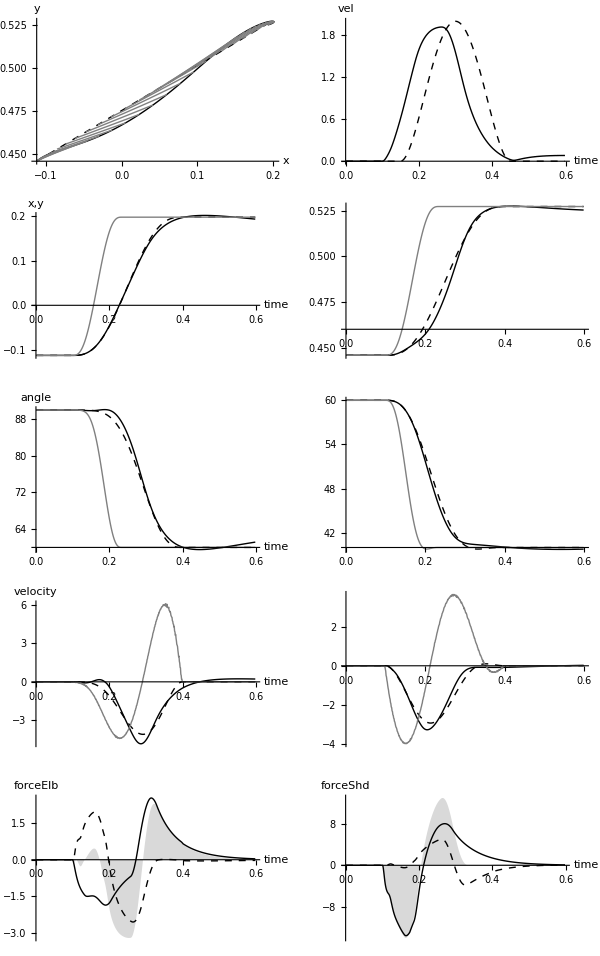

Reflex States

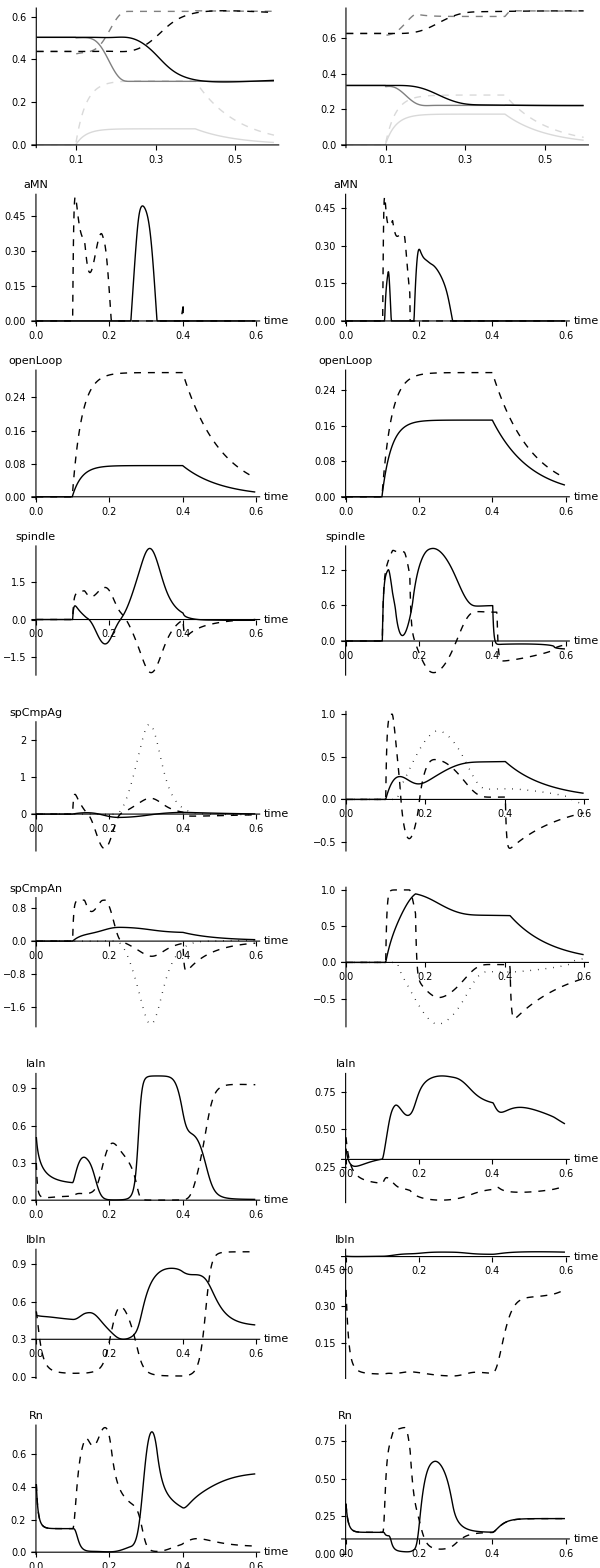

Muscle States

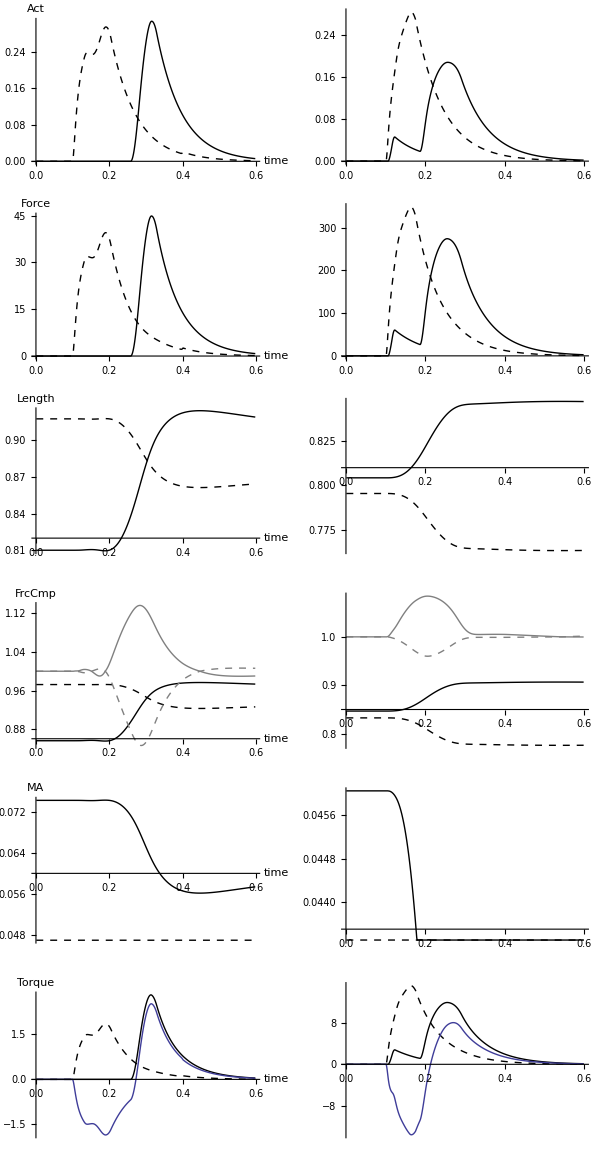

Phase space

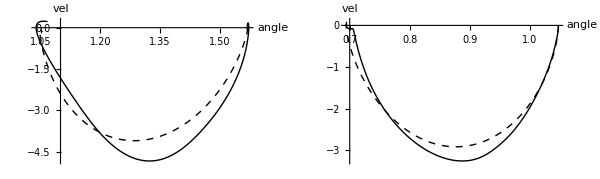

```mathematica
Print[Style["Arm States","Subtitle"]]
armPlots

Print[Style["Reflex States","Subtitle"]]
reflexPlots

Print[Style["Muscle States","Subtitle"]]
musclePlots

Print[Style["Phase space","Subtitle"]]
phSpacePlots
```

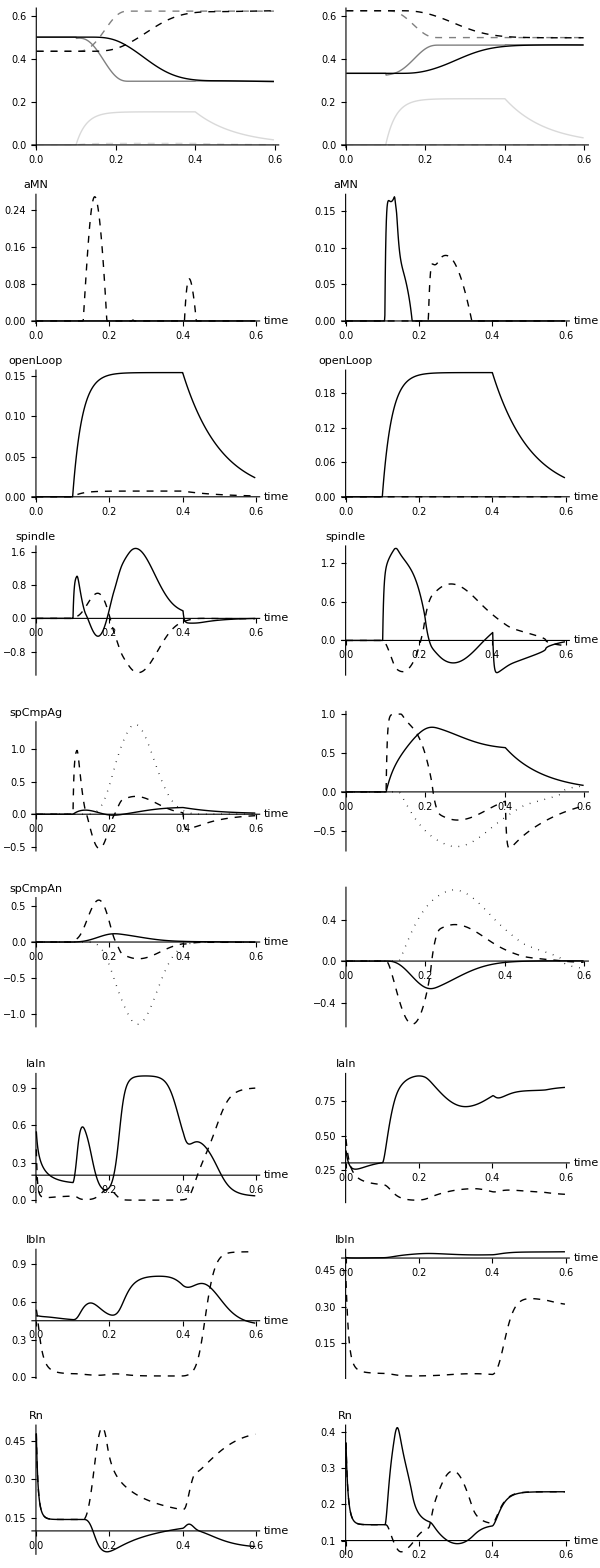

Muscle States

-Graphics-

Phase space

-Graphics-

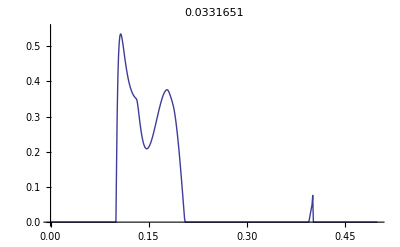

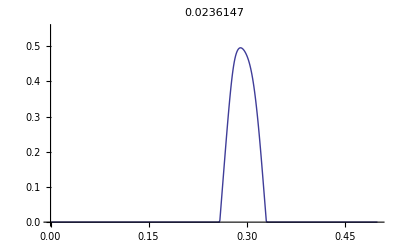

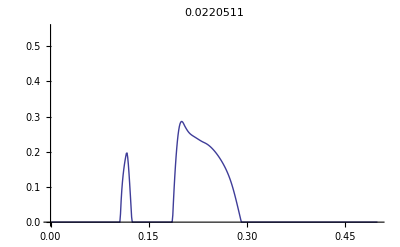

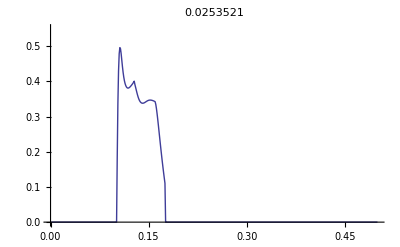

```mathematica
SetTrial[0];

ImpArea[tr_,var_,fr_,to_]:=Module[{},
SetTrial[tr];
s=NtoD[var];
s=s[[fr;;to]];
l=Length[s];
t = 0.001*Range[1,l];
d=ConstantArray[0.001,l];
ListLinePlot[Transpose[{t,s}],PlotRange->{Automatic,{0,0.55}},PlotLabel->Dot[d,s]]
];

ImpArea[0,"reflexElbMNAn",1,500]
ImpArea[0,"reflexElbMNAg",1,500]
ImpArea[0,"reflexShdMNAg",1,500]
ImpArea[0,"reflexShdMNAn",1,500]
```